```mathematica
DirectProduct[Z[2],Z[3]]//CayleyTable[#,Mode->Computational]&//StandardForm//Print
```

{{{0,0},{0,1},{0,2},{1,0},{1,1},{1,2}},{{0,1},{0,2},{0,0},{1,1},{1,2},{1,0}},{{0,2},{0,0},{0,1},{1,2},{1,0},{1,1}},{{1,0},{1,1},{1,2},{0,0},{0,1},{0,2}},{{1,1},{1,2},{1,0},{0,1},{0,2},{0,0}},{{1,2},{1,0},{1,1},{0,2},{0,0},{0,1}}}

-Graphics-

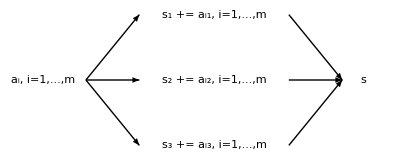

```mathematica
w=12;
p=2;
wh=7;
h=6;
{Text["a_i, i=1,...,m",{-w-p-2,0}],Arrow[{{-w,0},{-wh,h}}],Arrow[{{-w,0},{-wh,0}}],Arrow[{{-w,0},{-wh,-h}}],
Text["s_1 += a_i1, i=1,...,m",{0,h}],
Text["s_2 += a_i2, i=1,...,m",{0,0}],
Text["s_3 += a_i3, i=1,...,m",{0,-h}],
Arrow[{{wh,h},{w,0}}],
Arrow[{{wh,0},{w,0}}],
Arrow[{{wh,-h},{w,0}}],Text["s",{w+p,0}]}//Graphics
```